```mathematica
A =   
{{8, 1, 11},
{4, 0, 4}, 
{-4, -3, -7}};

B = {{-1}, {-3}, {3}};
x0={1,1,1};

r = 1.5; beta = -2.5;
K2 = {{-2.8182,0.9843,-2.8182}};

Acl2=A+B.K2;
xsol2[t_]=MatrixExp[Acl2 t].x0;
usol2[t_]=(K2.xsol2[t])[[1]];
eigs2=Eigenvalues[Acl2];
```

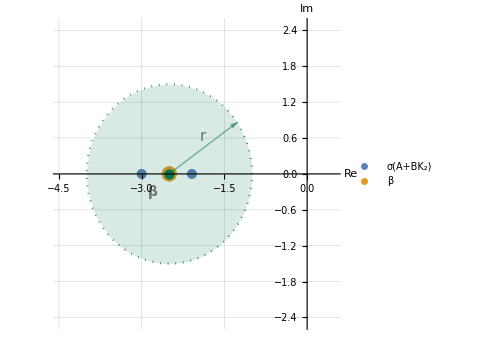

```mathematica
eigsPlot2 = Show[
ListPlot[
{{Re[#],Im[#]}&/@eigs2,{{beta,0}}},
PlotStyle->{{PointSize[0.02],SilverColor},{PointSize[0.03],GoldenrodYellow}},
PlotRange->{{-4.5,0.5},{-2.5,2.5}},
Axes->True,
AxesLabel->{Style["Re"],Style["Im"]},
LabelStyle->{FontFamily->"Times New Roman",FontSize->14},
PlotLegends->Placed[LineLegend[{"σ(A+BK₂)","β"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->14}],{0.65,0.95}],
GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],
AspectRatio->1, ImageSize->Medium
],

ParametricPlot[
{beta+r*Cos[t],r*Sin[t]},{t,0,2 Pi},
PlotStyle->{RGBColor[0.0,0.45,0.3],Dotted}
],

Graphics[
{RGBColor[0.0,0.45,0.3],Opacity[0.15],Disk[{beta,0},r],
RGBColor[0.0,0.45,0.3],Thick,Arrowheads[0.07],Opacity[0.5],
Arrow[{{beta,0},{beta+r*Cos[35 Degree],r*Sin[35 Degree]}}],
Black,Text[Style["r",FontSize->15,FontFamily->"Times New Roman"],
{beta+(r*Cos[35 Degree])/2,(r*Sin[35 Degree])/2+0.2}],
Black,Text[Style["β",FontSize->14,Bold, FontFamily->"Times New Roman"],{beta-0.3,-0.3}]}
],

Graphics[{RGBColor[0.0,0.45,0.3],PointSize[0.02],Point[{-2.51,0}]}] (*рисую руками, так как перекрыть желтую сложно.*)
]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/eig2.pdf"}],eigsPlot2];
```

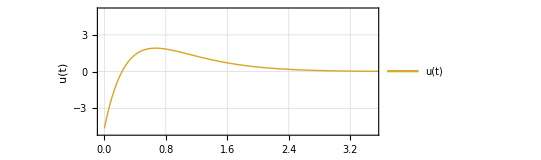

```mathematica
U2=Plot[{usol2[t]},{t,0,5},PlotStyle->{{RGBColor[0.85,0.65,0.13],Thick}},PlotLegends->Placed[LineLegend[{"u(t)"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.87,.9}],PlotRange->{{-0.02,3.5},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/U2.pdf"}],U2];
```

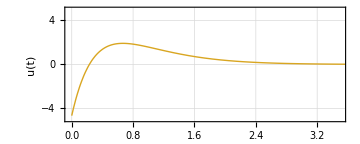

```mathematica
U2=Plot[usol2[t],{t,0,5},PlotStyle->{RGBColor[0.85,0.65,0.13],Thick},PlotLegends->Placed[LineLegend[{"u(t)"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.87,0.9}],PlotRange->{{-0.02,3.5},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/X2.pdf"}],X2];
```